```mathematica
SetOptions[FourierTransform,FourierParameters->{1,-1}];
```

```mathematica
(* Q6 *)
```

```mathematica
xt[τ_]=Piecewise[{{0,τ<1 || τ>3},{1,3>τ>1}}] ;(* INPUT *)
```

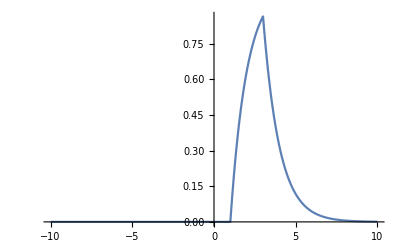

```mathematica
ht[τ_]:=Exp[-τ]*UnitStep[τ] (* Impulse Response *) 
yt[τ_]:=Convolve[ht[x],xt[x],x,τ]
Plot[yt[τ],{τ,-10,10},PlotRange->All]
```

```mathematica
Manipulate[Plot[{ht[(t-τ)],xt[τ]},{τ,-10,10},PlotRange->All,PlotStyle->{Orange,Black,Dashed}],{t,-5,7}]
```

```mathematica
Convolve[ht[τ],xt[τ],τ,y]
```

Piecewise[{{ⅇ^(1-y) (-1+ⅇ^2), y≥3}, {1-ⅇ^(1-y), 1<y<3}, {0, True}}]

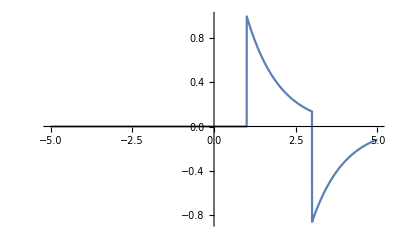

```mathematica
Plot[xt[τ]-yt[τ],{τ,-5,5},PlotRange->All]
```